Your Title Here

{{0,0,0.5},{0.2,0,0},{0,0.05,0.9}}

{{0,0,0},{0.2,0,0},{0,0.05,0.9}}

10

10

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

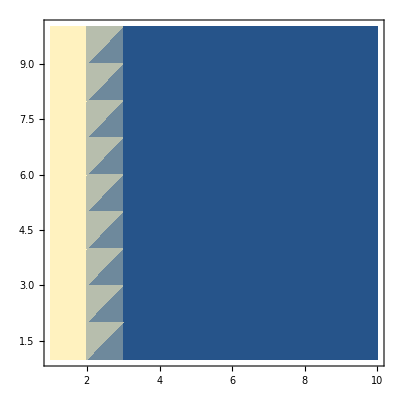

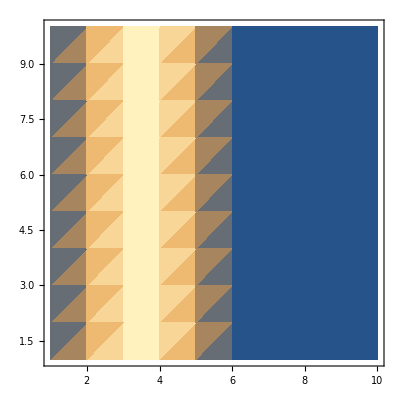

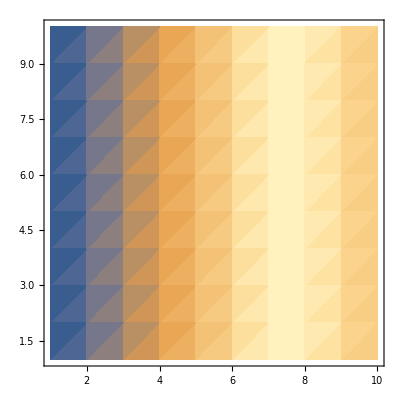

{{0,0,0},{0.2,0,0},{0,0.05,0.9}}

```mathematica
A = {{0 ,0,.5},{.2,0,0},{0,.05,.9}}
A2 = {{0 ,0,0},{.2,0,0},{0,.05,.9}}
gridSizeX = 10
gridSizeY = 10
ConstantArray[0,{gridSizeX ,gridSizeY}];
HSI1= ConstantArray[0,{gridSizeX,gridSizeY}];
HSI1[[1;; gridSizeX ,1;;2]]= 1;
HSISTORE[1] = HSI1;
Floor[gridSizeY*.3];
HSI2= ConstantArray[0,{gridSizeX,gridSizeY}];
insert1 = Array[#&,Floor[gridSizeY*.3],{0,2/3}];
insert2 = Array[#&,Floor[gridSizeY*.3],{2/3,0}];
Join[insert1,insert2];
HSI2[[1;; gridSizeX-1 ,1;;2*Floor[gridSizeY*.3]]] = Join[insert1,insert2];
HSI2[[gridSizeX,1;;2*Floor[gridSizeY*.3]]] = Join[insert1,insert2];
HSISTORE[2] = HSI2;
HSI3= ConstantArray[0,{gridSizeX,gridSizeY}]
insert3 = Array[#&,Floor[gridSizeY*.7],{0,2/3}];
insert4 = Array[#&,gridSizeY-Floor[gridSizeY*.7],{2/3,1/2}];
Join[insert3,insert4];
HSI3[[1;;gridSizeX-1,1;;gridSizeY]] = Join[insert3,insert4];
HSI3[[gridSizeX,1;;gridSizeY]] = Join[insert3,insert4];
HSISTORE[3] = HSI3;
ListDensityPlot[HSI1]
ListDensityPlot[HSI2]
ListDensityPlot[HSI3]
Clear[hospMat]
orig= ConstantArray[0,{2,4}];
hospMat= Table[orig,{i,gridSizeX},{j,gridSizeY}];
For[ki=1,ki≤2,ki++,
For[i=1,i≤gridSizeX,i++,
For[j=1,j≤gridSizeY,j++,
check=HSISTORE[ki+1][[i,j]];
If[i>1,hospMat[[i,j]][[ki,1]]=HSISTORE[ki+1][[i-1,j]]];
If[i<gridSizeX,hospMat[[i,j]][[ki,2]]=HSISTORE[ki+1][[i+1,j]]];
If[j>1,hospMat[[i,j]][[ki,3]]=HSISTORE[ki+1][[i,j-1]]];
If[j<gridSizeY,hospMat[[i,j]][[ki,4]]=HSISTORE[ki+1][[i,j+1]]];
]
]
]
T=100;
hospMat[[5,5,All,All]];
HSISTORE[2];
HSISTORE[3];
n= ConstantArray[{0,0,0},{gridSizeX,gridSizeY,T}];
spatMat = Table[ConstantArray[0,{3,3}],{i,gridSizeX},{j,gridSizeY} ];
spatMat[[1;;gridSizeX,1;;2]]=A;
spatMat[[1;;gridSizeX,3;;gridSizeY]]=A2;
spatMat[[2,10]]
n= ConstantArray[{0,0,0},{gridSizeX,gridSizeY,T}];
n[[1;;gridSizeX,Floor[gridSizeY/2],1,2]]=500;
n[[1;;gridSizeX,Floor[gridSizeY/2],1,3]]=500;
totpop [1]= Total[Total[n[[All,All,1,3]]]];
toteggs[1] = Total[Total[n[[All,All,1,1]]]];
totchild[1] = Total[Total[n[[All,All,1,2]]]];
CC = 1000;

For[t=2,t≤T,t++,
For[xloc=1,xloc≤gridSizeX,xloc++,
For[yloc=1,yloc≤gridSizeY,yloc++,
	A=spatMat[[xloc,yloc]];
	n[[xloc,yloc,t,All]]=A.n[[xloc,yloc,t-1,All]];
	(*n[[xloc,yloc,t,All]]=n[[xloc,yloc,t-1,All]];*)
	];
];
(*migrate all cells*)
migDirStore = ConstantArray[{0,0},{gridSizeX,gridSizeY}];
migrantsAll = ConstantArray[{0,0},{gridSizeX,gridSizeY}];

For[xloc=1,xloc≤gridSizeX,xloc++,
For[yloc=1,yloc≤gridSizeY,yloc++,
thishospMat=hospMat[[xloc,yloc,All, All]];
CC2val=1-(n[[xloc,yloc,t,2]])/(n[[xloc,yloc,t,2]]+CC);
CC3val=1-(n[[xloc,yloc,t,3]])/(n[[xloc,yloc,t,3]]+CC);
migrantsThisCell={(1-HSISTORE[2][[xloc,yloc]])*CC2val*Random[]*n[[xloc,yloc,t,2]],(1-HSISTORE[3][[xloc,yloc]])*CC3val*Random[]*n[[xloc,yloc,t,3]]};
migDir=migrantsThisCell*(thishospMat);
migrantsThisCell=Total[migDir,{2}];
migDirStore[[xloc,yloc,All]]=migrantsThisCell;
If[xloc>1,migrantsAll[[xloc-1,yloc,All]]=migrantsAll[[xloc-1,yloc,All]]+migDir[[All,1]]];
If[xloc<gridSizeX,migrantsAll[[xloc+1,yloc,All]]=migrantsAll[[xloc+1,yloc,All]]+migDir[[All,2]]];
If[yloc>1,migrantsAll[[xloc,yloc-1,All]]=migrantsAll[[xloc,yloc-1,All]]+migDir[[All,3]]];
If[yloc<gridSizeY,migrantsAll[[xloc,yloc+1,All]]=migrantsAll[[xloc,yloc+1,All]]+migDir[[All,4]]];
];
];
n[[All,All,t,2]]=n[[All,All,t,2]]-migDirStore[[All,All,1]]+migrantsAll[[All,All,1]];
n[[All,All,t,3]]=n[[All,All,t,3]]-migDirStore[[All,All,2]] + migrantsAll[[All,All,2]];
totpop [t] = Total[Total[n[[All,All,t,3]]]];
toteggs[t] = Total[Total[n[[All,All,t,1]]]];
totchild[t] = Total[Total[n[[All,All,t,2]]]];
];
```

```mathematica
Manipulate[
Grid[
{
{ListDensityPlot[n[[All,All,Floor@t,1]],InterpolationOrder->0,PlotRange->All,ImageSize->{200,200}, PlotLabel->"egg density distribution"],
ListDensityPlot[n[[All,All,Floor@t,2]],InterpolationOrder->0,PlotRange->All,ImageSize->{200,200}, PlotLabel->"children density distribution"],
ListDensityPlot[n[[All,All,Floor@t,3]],InterpolationOrder->0,PlotRange->All,ImageSize->{200,200}, PlotLabel->"adults density distribution"]},

{p1 = ListPlot[n[[X,Y,1;;t,1]],Joined->True];p2 = ListPlot[n[[X,Y,1;;t,2]],Joined->True];p3 = ListPlot[n[[X,Y,1;;t,3]],Joined->True];
Show[p1,p2,p3,PlotRange->All,ImageSize->{200,200}],
Text["the total number of adults at year " <> ToString[t] <> " is "  <> ToString[totpop[t]]]
Text["the total number of children at year " <> ToString[t] <> " is "  <> ToString[totchild[t]]]
Text["the total number of Eggs at year " <> ToString[t] <> " is "  <> ToString[toteggs[t]]] },

{DiscretePlot[toteggs[j], {j,1,T},ImageSize->{200,200}, PlotLabel->"total egg"],DiscretePlot[totchild[j], {j,1,T},ImageSize->{200,200}, PlotLabel->"total children"],DiscretePlot[totpop[j], {j,1,T},ImageSize->{200,200}, PlotLabel->"total adults"]}
}
]
,{t,1,T,1},{X,1,gridSizeX,1},{Y,1,gridSizeY,1},ContentSize->{800,650}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

General::stop: Further output of ListDensityPlot::arrayerr will be suppressed during this calculation.

Part::partd: Part specification n⟦5,4,1;;21,1⟧ is longer than depth of object.

ListPlot::lpn: n⟦5,4,1;;21,1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification n⟦5,4,1;;21,2⟧ is longer than depth of object.

ListPlot::lpn: n⟦5,4,1;;21,2⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification n⟦5,4,1;;21,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[n⟦5,4,1;;21,1⟧,Joined→True],ListPlot[n⟦5,4,1;;21,2⟧,Joined→True],ListPlot[n⟦5,4,1;;21,3⟧,Joined→True],PlotRange→All,ImageSize→{200,200}].

DiscretePlot::iterb: Iterator {j,1,T} does not have appropriate bounds.

General::stop: Further output of DiscretePlot::iterb will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

General::stop: Further output of ListDensityPlot::arrayerr will be suppressed during this calculation.

Part::partd: Part specification n⟦5,4,1;;21,1⟧ is longer than depth of object.

ListPlot::lpn: n⟦5,4,1;;21,1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification n⟦5,4,1;;21,2⟧ is longer than depth of object.

ListPlot::lpn: n⟦5,4,1;;21,2⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification n⟦5,4,1;;21,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[n⟦5,4,1;;21,1⟧,Joined→True],ListPlot[n⟦5,4,1;;21,2⟧,Joined→True],ListPlot[n⟦5,4,1;;21,3⟧,Joined→True],PlotRange→All,ImageSize→{200,200}].

DiscretePlot::iterb: Iterator {j,1,T} does not have appropriate bounds.

General::stop: Further output of DiscretePlot::iterb will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

General::stop: Further output of ListDensityPlot::arrayerr will be suppressed during this calculation.

Part::partd: Part specification n⟦5,4,1;;21,1⟧ is longer than depth of object.

ListPlot::lpn: n⟦5,4,1;;21,1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification n⟦5,4,1;;21,2⟧ is longer than depth of object.

ListPlot::lpn: n⟦5,4,1;;21,2⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification n⟦5,4,1;;21,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[n⟦5,4,1;;21,1⟧,Joined→True],ListPlot[n⟦5,4,1;;21,2⟧,Joined→True],ListPlot[n⟦5,4,1;;21,3⟧,Joined→True],PlotRange→All,ImageSize→{200,200}].

DiscretePlot::iterb: Iterator {j,1,T} does not have appropriate bounds.

General::stop: Further output of DiscretePlot::iterb will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

General::stop: Further output of ListDensityPlot::arrayerr will be suppressed during this calculation.

Part::partd: Part specification n⟦5,4,1;;21,1⟧ is longer than depth of object.

ListPlot::lpn: n⟦5,4,1;;21,1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification n⟦5,4,1;;21,2⟧ is longer than depth of object.

ListPlot::lpn: n⟦5,4,1;;21,2⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification n⟦5,4,1;;21,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[n⟦5,4,1;;21,1⟧,Joined→True],ListPlot[n⟦5,4,1;;21,2⟧,Joined→True],ListPlot[n⟦5,4,1;;21,3⟧,Joined→True],PlotRange→All,ImageSize→{200,200}].

DiscretePlot::iterb: Iterator {j,1,T} does not have appropriate bounds.

General::stop: Further output of DiscretePlot::iterb will be suppressed during this calculation.

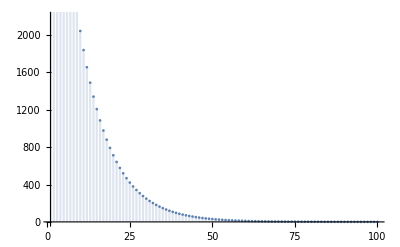

0.157897

```mathematica
DiscretePlot[totpop[j], {j,1,T}]
totpop[100]
```

Visualize the dispersion and population dynamics of Logger head sea turtles by integrating a system of Leslie Matrices.

-Graphics-

-Graphics--Graphics--Graphics--Graphics-

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: Aravind Sundararajan